# Метод на хордите

Задача: Дадено е уравенението:
x^2+  px − (q + 50) cos x − 2(p + q) = 0, където p и q са съответно предпоследната и последната цифра от факултетния ни номер (в случая p = 1 а q = 9)
x^2 + x − 59 cos x − 20 = 0
	 1.  Да се намери общия брой на корените на уравнението.
2. Да се локализира най-големия реален корен в интервала [a, b]. 
3. Да се проверят условията за приложение на метода на хордите.
		- проверка на сходимост
		- избор на начално приближение и постоянна точка
		- итерациите
	 4.  Да се изчисли корена по метода на хордите с точност 10^-4. Представете таблица с изчисленията.
	 5.  Да се провери колко итерации биха били необходими, ако се използва метода на разполовяването в същия интервал [a, b] за същата точност.
6.  Да се направи сравнение кой метод е по-ефективен за избрания интервал.

```mathematica
f[x_] := x^2 +x - 59 Cos[x] - 20
```

```mathematica
f[x]
```

-20+x+x^2-59 Cos[x]

## 1. Да се намери общия брой на корените на уравнението

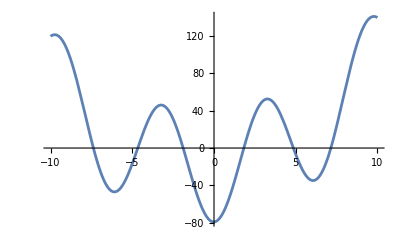

```mathematica
Plot[f[x], {x, -10, 10}]
```

Брой корени: 6

## 2. Да се локализира най-големия реален корен в интервала [a, b]

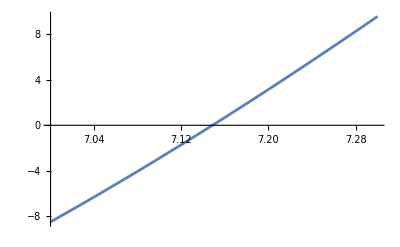

```mathematica
Plot[f[x], {x, 7, 7.3}]
```

```mathematica
f[7.]
```

-8.48023

```mathematica
f[7.3]
```

9.55143

Извод:
(1) Функцията е непрекъсната, защото е сума от непрекъснати функции (полином и синус).
(2) f(5) = -8.460 ... < 0
       f(7) = 9.551 ... > 0
       => Функцията има различни знаци в двата края на разглеждания интервал [7; 7.3].
       От (1) и (2) следва, че функцията има поне един корен в разглеждания интервал [7; 7.3].

## 3. Да се проверят условията за приложение на метода на хордите

### Проверка на сходимост

#### Графика на първата производна

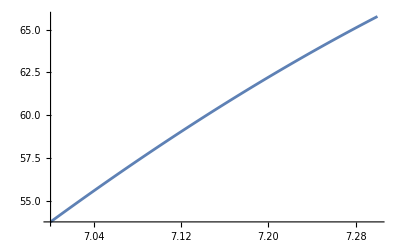

```mathematica
Plot[f'[x],{x,7.,7.3}]
```

Извод: (1) Стойностите на първата производна в разглеждания интервал [7.,7.3] са между 53 и 66. Следователно първата f'(x) > 0 в целия разглеждан интервал [7.,7.3].

#### Графика на втората производна

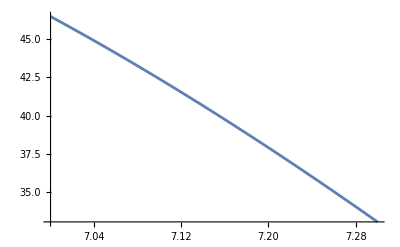

```mathematica
Plot[f''[x],{x,7.,7.3}]
```

Извод : (2) Стойностите на втората производна в разглеждания интервал [7.,7.3] са между 47 и 33. Следователно втората f'' (x) > 0 в целия разглеждан интервал [] .

Извод: От (1) и (2) следва, че първата и втората производна имат постоянни знаци в разглеждания интервал [7.,7.3]. Следователно условията за сходимост на метода на хордите са изпълнени.

### Избор на начално приближение и постоянна точка

Нужно е да е изпълнено условието f(x0).f’’(x) < 0
В нашия случай f’’(x) >0. Следователно е нужно f(x0) <0

```mathematica
p = 7.
```

7.

```mathematica
x0 = 7.3
```

7.3

### Итериране

```mathematica
For[n = 0, n <= 10, n++,
x1 = x0 - f[x0]/(f[x0] - f[p])*(x0 - p);
Print["n = ",n,  " x_n = ", x1];
x0 = x1
]
```

n = 0 x_n = 7.14109

n = 1 x_n = 7.14902

n = 2 x_n = 7.14858

n = 3 x_n = 7.1486

n = 4 x_n = 7.1486

n = 5 x_n = 7.1486

n = 6 x_n = 7.1486

n = 7 x_n = 7.1486

n = 8 x_n = 7.1486

n = 9 x_n = 7.1486

n = 10 x_n = 7.1486

## 4. Да се изчисли корена по метода на хордите с точност 10^-4

### Изчисляване на постоянните величини

```mathematica
Plot[Abs[f'[x]],{x,7.,7.3}]
```

-Graphics-

От геометрично съображение минимума на абсолютната стойност на първата производна се достига в левия край на интервала, а максимума - в десния.

```mathematica
M1 = Abs[f'[7.]]
```

53.7622

```mathematica
m1 = Abs[f'[7.3]]
```

65.7758

```mathematica
R = (M1 - m1)/m1
```

-0.182644

```mathematica
f[x_] := x^2 +x - 59 Cos[x] - 20
p = 7.; x0 = 7.3;
M1 = Abs[f'[7.]];
m1 = Abs[f'[7.3]];
R = (M1 - m1)/m1;
For[n = 0, n <= 10, n++,
x1 = x0 - f[x0]/(f[x0] - f[p])*(x0 - p);
Print["n = ",n,  " x_n = ", x1, " f(x_n) = ", f[x1], " ε_n = ", eps = R * Abs[x1 - x0]];
x0 = x1
]
```

n = 0 x_n = 7.14109 f(x_n) = -0.451213 ε_n = -0.0290241

n = 1 x_n = 7.14902 f(x_n) = 0.0251114 ε_n = -0.00144816

n = 2 x_n = 7.14858 f(x_n) = -0.00138575 ε_n = -0.0000803568

n = 3 x_n = 7.1486 f(x_n) = 0.0000765069 ε_n = -4.43514×10^-6

n = 4 x_n = 7.1486 f(x_n) = -4.22383×10^-6 ε_n = -2.44861×10^-7

n = 5 x_n = 7.1486 f(x_n) = 2.33191×10^-7 ε_n = -1.35184×10^-8

n = 6 x_n = 7.1486 f(x_n) = -1.28741×10^-8 ε_n = -7.46332×10^-10

n = 7 x_n = 7.1486 f(x_n) = 7.10763×10^-10 ε_n = -4.12038×10^-11

n = 8 x_n = 7.1486 f(x_n) = -3.92433×10^-11 ε_n = -2.27482×10^-12

n = 9 x_n = 7.1486 f(x_n) = 2.14584×10^-12 ε_n = -1.25559×10^-13

n = 10 x_n = 7.1486 f(x_n) = -9.9476×10^-14 ε_n = -6.81326×10^-15

Цикъл със стоп-критерий при определена точност (в случая ε_n  = 0.0001)

```mathematica
f[x_] := x^2 +x - 59 Cos[x] - 20
p = 7.; x0 = 7.3;
M1 = Abs[f'[7.]];
m1 = Abs[f'[7.3]];
R = (M1 - m1)/m1;
epszad = 0.0001;
eps = 1;
Print["n = ",0,  " x_n = ", x0, " f(x_n) = ", f[x0]];
For[n = 1, eps > epszad, n++,
x1 = x0 - f[x0]/(f[x0] - f[p])*(x0 - p);
Print["n = ",n,  " x_n = ", x1, " f(x_n) = ", f[x1], " ε_n = ", eps = R * Abs[x1 - x0]];
x0 = x1
]
```

n = 0 x_n = 7.3 f(x_n) = 9.55143

n = 1 x_n = 7.14109 f(x_n) = -0.451213 ε_n = -0.0290241

## 5. Да се провери колко итерации биха били необходими, ако се използва метода на разполовяването в същия интервал [a, b] за същата точност.

```mathematica
Log2[(7.3 - 7)/0.0001] - 1
```

10.5507

## 6. Да се направи сравнение кой метод е по-ефективен за избрания интервал

Извод: По метода на разполовяването биха били необходими 11 итерации за достигане на исканата точност. А по метода на хордите беше необходима само 1 итерация. Следователно методът на хордите е по-ефективен за избрания интервал [7, 7.3].